# Mosquito population dynamics include Early instars, layter instars, pupae, and adults female.

## How to use

Using the code here we can determine seasonal patterns in infection and test the effect of IRS on the mosquito populations. This is a deterministic implementation of the model by White et al. 2011, which itself relies on other references and particularly Griffin et al. 2010. The workflow is to feed the function here the seasonal and or IRS scheme that we want and to take the output and feed it to the parameter file of the ABM. The final vector should be normalized by the predicted abundance without an intervention, to get the amplitude to multiply the biting rate parameter in the model.

White MT, Griffin JT, Churcher TS, Ferguson NM, Basáñez M-G, Ghani AC. Modelling the impact of vector control interventions on Anopheles gambiae population dynamics. Parasit Vectors. 2011;4: 153.

```mathematica
ClearAll[A,P,L,M,K,f,MuM,MuE,MuL, c, TimeMax];
```

## Carrying capacity

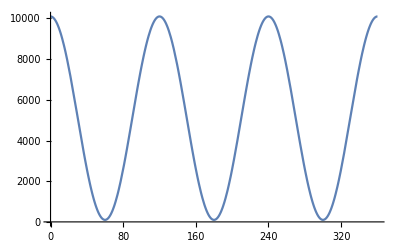

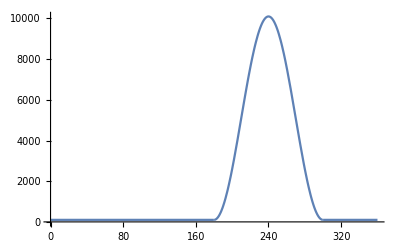

```mathematica
K[t_]:=10000*(0.5+0.5*Sin[2π*(t/120+30/120)])+100; (* Carrying capacity is just a sin function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. the 10000 is just an arbitrary number. Carrying capacity is just for the first 2 stages, as their mortality rates depend on carrying capacity *)
f[t_]:=Piecewise[{{K[t],180<Mod[t,360]<300}},100];  (*Seasonality in carrying capacity. In the rainy season (days 180 to 300, calculate K. Otherwise set to a baseline of 100*)
f[t_]:=Piecewise[{{K[t],180<Mod[t,360]<300}},100];
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

## Mortality rates

### Non - adult mortality rates

```mathematica
(* MuE and MuL are the daily mortality of eggs+early larvae and of late larva stages, respectively. 
Both are density-dependent on the number of early and late larva stages, calculated as (A+L)/f, where f is the environmental carrying capacity at time t; 
\mu_E^0 and \mu_L^0 are assumed to be 0.035 and γ = 13.25. These values are taken from Table 1.
The equations are Eq. 7 in the paper.
*)
```

```mathematica
MuE[t_]:=0.035*(1+(A[t]+L[t])/f[t]); 
MuL[t_]:=0.035*(1+13.25*(A[t]+L[t])/f[t]);
```

### Adult mortality rates -- this is the definition of the intervention

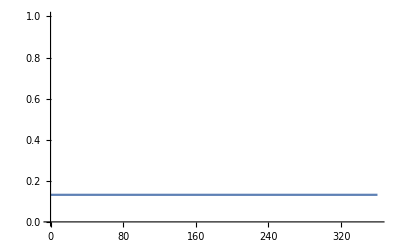

0.8

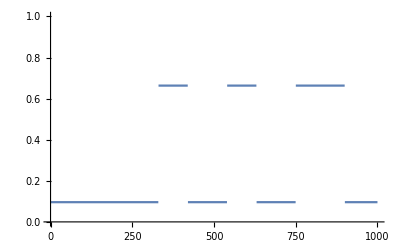

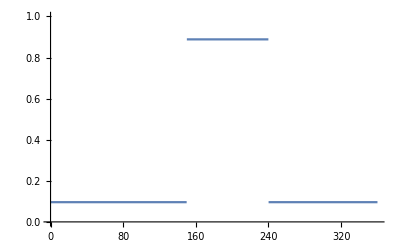

```mathematica
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)

(*MuM is the daily mortality rate of adult mosquitos.The Log turns the w into a rate.*)

(* Example 0: No external mortality rates (no IRS), so c=0 *)
c=0;
TimeMax=360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= {-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,0<t<TimeMax};
Plot[Evaluate[MuM[0,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]

(* Example 1: Our Ghana data. Assume c=0.8 *)
c=0.8
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,330<t<420||540<t<630||750<t<900}},MuM0]; (* The part of 330<t<420||540<t<630||750<t<900 is the IRS scheme of our Ghana data. *)
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,1000},PlotRange->{0,1}]


(* Example 2: IRS of 3 months, May-July, with c=0.9 *)
c=0.9;
TimeMax=360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,150<t<240}},MuM0];
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]
(* Plot the mortality rates *)
```

## Mosquito population dynamics with IRS

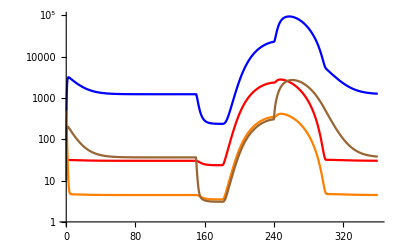

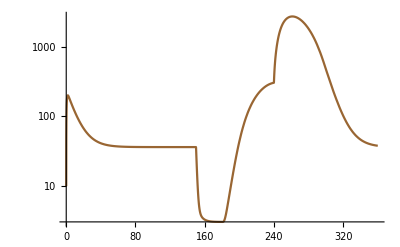

```mathematica
(* Need to set the IRS scheme, so change these next three lines as necessary *)
TimeMax=360;
c=0.9;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,150<t<240}},MuM0];

β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[c,0.92,0.97,0.207,0.86,t]*M[t], (*Adult mosquitos, half of them are female*)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown}] (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];(* Obtain mosquito abundance with intervention*)
```

## Mosquito population dynamics without IRS (only seasonality)

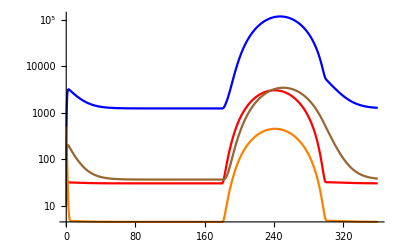

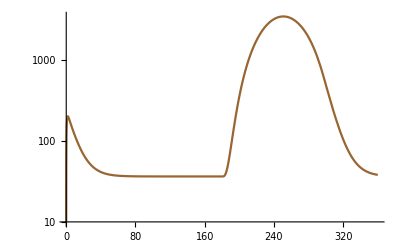

```mathematica
(* When there is no IRS then the mortality rate of adults is just the basline MuM0. This goes in the calculation of M'[t] *)

β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM0*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
MosquitoNoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];
```

## Export to a file

{{0,10.},{1,184.982},{2,200.255},{3,190.092},{4,176.937},{5,164.343},{6,152.794},{7,142.28},{8,132.722},{9,124.034},{10,116.136},{11,108.956},{12,102.43},{13,96.4955},{14,91.0999},{15,86.1935},{16,81.7316},{17,77.6735},{18,73.9824},{19,70.6246},{20,67.5698},{21,64.7903},{22,62.261},{23,59.9592},{24,57.864},{25,55.9568},{26,54.2205},{27,52.6395},{28,51.1998},{29,49.8887},{30,48.6944},{31,47.6065},{32,46.6153},{33,45.7123},{34,44.8893},{35,44.1394},{36,43.4558},{37,42.8327},{38,42.2648},{39,41.747},{40,41.2748},{41,40.8444},{42,40.4518},{43,40.0938},{44,39.7673},{45,39.4695},{46,39.1979},{47,38.9502},{48,38.7242},{49,38.518},{50,38.3299},{51,38.1583},{52,38.0018},{53,37.8589},{54,37.7286},{55,37.6097},{56,37.5012},{57,37.4022},{58,37.3118},{59,37.2294},{60,37.1541},{61,37.0855},{62,37.0228},{63,36.9656},{64,36.9135},{65,36.8658},{66,36.8224},{67,36.7827},{68,36.7465},{69,36.7135},{70,36.6833},{71,36.6558},{72,36.6307},{73,36.6078},{74,36.5868},{75,36.5677},{76,36.5503},{77,36.5344},{78,36.5199},{79,36.5066},{80,36.4946},{81,36.4835},{82,36.4734},{83,36.4642},{84,36.4559},{85,36.4482},{86,36.4412},{87,36.4348},{88,36.429},{89,36.4237},{90,36.4188},{91,36.4144},{92,36.4104},{93,36.4067},{94,36.4033},{95,36.4002},{96,36.3974},{97,36.3949},{98,36.3925},{99,36.3904},{100,36.3884},{101,36.3867},{102,36.3851},{103,36.3836},{104,36.3822},{105,36.381},{106,36.3799},{107,36.3788},{108,36.3779},{109,36.377},{110,36.3763},{111,36.3755},{112,36.3749},{113,36.3743},{114,36.3738},{115,36.3733},{116,36.3728},{117,36.3724},{118,36.372},{119,36.3717},{120,36.3714},{121,36.3711},{122,36.3708},{123,36.3706},{124,36.3704},{125,36.3702},{126,36.37},{127,36.3698},{128,36.3697},{129,36.3695},{130,36.3694},{131,36.3693},{132,36.3692},{133,36.3691},{134,36.369},{135,36.3689},{136,36.3688},{137,36.3688},{138,36.3687},{139,36.3687},{140,36.3686},{141,36.3686},{142,36.3685},{143,36.3685},{144,36.3685},{145,36.3684},{146,36.3684},{147,36.3684},{148,36.3683},{149,36.3683},{150,36.3683},{151,36.3683},{152,36.3683},{153,36.3682},{154,36.3682},{155,36.3682},{156,36.3682},{157,36.3682},{158,36.3682},{159,36.3682},{160,36.3682},{161,36.3682},{162,36.3682},{163,36.3682},{164,36.3681},{165,36.3681},{166,36.3681},{167,36.3681},{168,36.3681},{169,36.3681},{170,36.3681},{171,36.3681},{172,36.3681},{173,36.3681},{174,36.3681},{175,36.3681},{176,36.3681},{177,36.3681},{178,36.3681},{179,36.3681},{180,36.3681},{181,36.3824},{182,36.5869},{183,37.3137},{184,38.8897},{185,41.5969},{186,45.6777},{187,51.3463},{188,58.8024},{189,68.2405},{190,79.8547},{191,93.8398},{192,110.387},{193,129.677},{194,151.877},{195,177.13},{196,205.557},{197,237.249},{198,272.269},{199,310.653},{200,352.409},{201,397.521},{202,445.948},{203,497.63},{204,552.487},{205,610.42},{206,671.317},{207,735.048},{208,801.474},{209,870.442},{210,941.787},{211,1015.34},{212,1090.91},{213,1168.32},{214,1247.36},{215,1327.84},{216,1409.54},{217,1492.26},{218,1575.77},{219,1659.86},{220,1744.3},{221,1828.87},{222,1913.35},{223,1997.5},{224,2081.11},{225,2163.95},{226,2245.8},{227,2326.43},{228,2405.63},{229,2483.19},{230,2558.9},{231,2632.55},{232,2703.94},{233,2772.88},{234,2839.19},{235,2902.68},{236,2963.19},{237,3020.54},{238,3074.59},{239,3125.19},{240,3172.19},{241,3215.48},{242,3254.94},{243,3290.45},{244,3321.93},{245,3349.28},{246,3372.44},{247,3391.34},{248,3405.93},{249,3416.18},{250,3422.05},{251,3423.53},{252,3420.62},{253,3413.33},{254,3401.67},{255,3385.69},{256,3365.42},{257,3340.92},{258,3312.26},{259,3279.52},{260,3242.8},{261,3202.18},{262,3157.79},{263,3109.75},{264,3058.18},{265,3003.24},{266,2945.07},{267,2883.84},{268,2819.71},{269,2752.86},{270,2683.48},{271,2611.75},{272,2537.88},{273,2462.07},{274,2384.53},{275,2305.46},{276,2225.1},{277,2143.66},{278,2061.37},{279,1978.46},{280,1895.15},{281,1811.68},{282,1728.28},{283,1645.17},{284,1562.6},{285,1480.78},{286,1399.96},{287,1320.35},{288,1242.18},{289,1165.66},{290,1091.02},{291,1018.46},{292,948.195},{293,880.42},{294,815.333},{295,753.124},{296,693.975},{297,638.064},{298,585.559},{299,536.622},{300,491.402},{301,450.016},{302,412.355},{303,378.128},{304,347.029},{305,318.774},{306,293.101},{307,269.775},{308,248.58},{309,229.322},{310,211.822},{311,195.921},{312,181.47},{313,168.339},{314,156.405},{315,145.559},{316,135.702},{317,126.742},{318,118.598},{319,111.194},{320,104.464},{321,98.3453},{322,92.7819},{323,87.723},{324,83.1226},{325,78.9387},{326,75.1332},{327,71.6715},{328,68.5223},{329,65.657},{330,63.0497},{331,60.677},{332,58.5174},{333,56.5516},{334,54.762},{335,53.1326},{336,51.6489},{337,50.2976},{338,49.0669},{339,47.9458},{340,46.9245},{341,45.994},{342,45.1461},{343,44.3733},{344,43.6691},{345,43.0271},{346,42.442},{347,41.9085},{348,41.4222},{349,40.9787},{350,40.5743},{351,40.2055},{352,39.8692},{353,39.5625},{354,39.2827},{355,39.0275},{356,38.7947},{357,38.5824},{358,38.3886},{359,38.2119},{360,38.0506}}

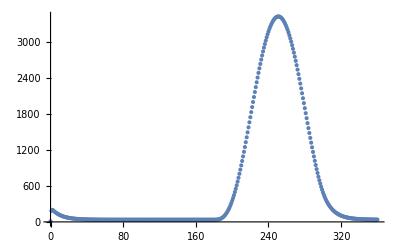

```mathematica
(* MosquitoAbundaceNormalized=MosquitoIRS/MosquitoNoIRS;  *)
data=Transpose@{Range[0,TimeMax],Flatten[MosquitoNoIRS,2]}
ListPlot[data]
```